# Modified coupling parameter

## Normalized variables

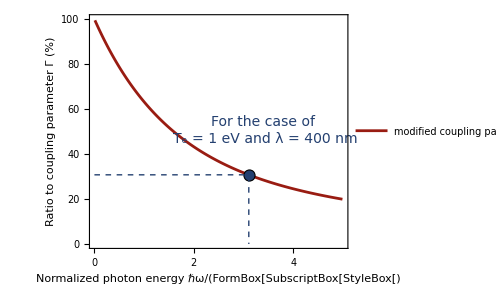

```mathematica
(* -- data -- *)
Γ=1;
Γω[x_]:=Γ(1/x)(1-Exp[-x]);
dt=Table[{x,Γω[x]},{x,.01,4.99,.01}];

sel=6.626*^-34*3*^8/400*^-9/1.6*^-19; (* When, Subscript[T, e] = 1 eV, λ = 400 nm *)
pt={sel,Γω[sel]};

(* -- plot -- *)
gf=ListLinePlot[

dt,

Epilog->{
Text[Style[StringForm["For the case of \n`1` = 1 eV and λ = 400 nm",Subscript[Style["T",Italic],"e"]],{FontColor->RGBColor[.14,.25,.44,1],FontSize->14,FontWeight->Plain,TextAlignment->Left}],pt+{.33,.13},{0,-1}],
{EdgeForm[Transparent],FaceForm[{RGBColor[.14,.25,.44,1]}],Disk[pt,Offset[4]]},
{RGBColor[.14,.25,.44,1],AbsoluteThickness[1],AbsoluteDashing[4],Line[{{0,pt[[2]]},pt,{pt[[1]],0}}]}
},

Joined->True,
PlotRange->{{0,5},{0,1}},
PlotRangePadding->0,

PlotStyle->{
{RGBColor[.60,.11,.07,1],Opacity[1],AbsoluteThickness[2]}
},

PlotLegends->Placed[LineLegend[
{StringForm["modified coupling parameter `1`",Subscript["Γ","ω"]]},
LegendLayout->"Column"],{{.97,.92},{1,1}}],

Axes->False,
Frame->True,
FrameLabel->{{"Ratio to coupling parameter Γ (%)",None},{StringForm["Normalized photon energy (<ℏω>)/(`1``2`)",Subscript[Style["k",Italic],"B"],Subscript[Style["T",Italic],"e"]],None}},
FrameTicks->{
{Table[{i/100,If[Mod[i,20]==0,i,Null],{If[Mod[i,20]==0,.015,.008],0}},{i,0,100,5}],
Table[{i/100,Null,{If[Mod[i,20]==0,.015,.008],0}},{i,0,100,5}]},
{Table[{i/10,If[Mod[i,10]==0,i/10,Null],{If[Mod[i,10]==0,.015,.008],0}},{i,0,50,5}],
Table[{i/10,Null,{If[Mod[i,10]==0,.015,.008],0}},{i,0,50,5}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,

PlotRangeClipping->False,
(*ImagePadding->{{55,5},{45,15}},*)
ImageSize->(65*2)*(72/25.4),
AspectRatio->.8

];

Print[gf];

Export[NotebookDirectory[]<>"modifiedGamma.pdf",gf];
```